```mathematica
minkowski=Plot[{x/3,3x},{x,-3,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotStyle->{{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed},{Thickness->Absolute[0.2],LineColor->GrayLevel[0.4],Dashed}},Ticks->None,PlotRangeClipping->False,AxesLabel->{t,x},Epilog->{GrayLevel[0.4],Text[Style[OverBar[t]],{3.4,1.15}],Text[Style[OverBar[x]],{1.15,3.4}]},ImageSize->Small]
```

-Graphics-

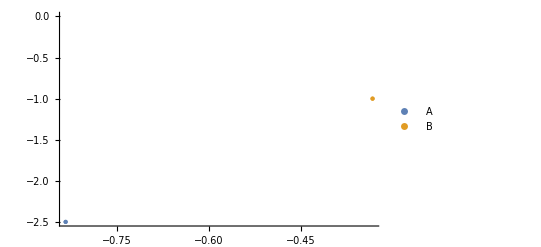

```mathematica
P4a=ListPlot[{{{-2.5/3,-2.5}},{{-1/3,-1}}},PlotStyle->{PointSize[Large]},PlotLegends->{A,B}]
```

```mathematica
lines={Graphics[{Thin,Dotted,Line[{{-1/3,-1},{-1/3,0}}]}],Graphics[{Thin,Dotted,Line[{{-2.5/3,-2.5},{-2.5/3,0}}]}]}
```

{-Graphics-,-Graphics-}

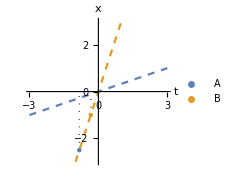

```mathematica
Show[minkowski,lines,P4a]
```